# Calculating AVS Curves

## QEA Boats Module

By Dieter Brehm & Sam Sam Daitzman

## Explanation

### This file contains Mathematica code for calculating the RM curve of a differently shaped three dimensional boats. First, we define our desired boats. Then, we define a function for finding the moment at a given heal angle. Finally, we map that function to several angles and generate a plot.

## Code

Defining and showing a plot of the two boats

```mathematica
boat = ImplicitRegion[(x)^2/(10.16)^2+(y-18.24)^2/(18.24)^2 +z^2/(15.32)^2<1 && y < 15.24,{ {x,-20,20},{y,-20,20},{z,-50,50}}];
```

```mathematica
Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x(cm)","y(cm)","z(cm)"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]]]
```

-Graphics3D-

Code for calculating moment of arbitrary ImplicitRegion boat at a heel angle

```mathematica
boatmass[boatregion_, density_] :=
 mass = N[(Volume[boatregion]*density)+900.,5]
boatcom[boatregion_, density_] := 
com = N[ 1/(boatmass[boatregion, density]+900.)*NIntegrate[density*{x,y,z}, {x,y,z}∈boatregion],5]
moment[hullshape_,mass_,com_,density_, theta_]:= Module[{},
rads = theta * (Pi/180);
water = ImplicitRegion[If[rads<Pi / 2,y<Tan[rads ]*x+18.24+d,y>Tan[rads ]*x+18.24+d],{ {x,-20,20},{y,-20,20},{z,-25,25}}];
under = RegionIntersection[hullshape, water];
disp = Integrate[1, {x,y,z}∈under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = RegionCentroid[under/.{d->draft}];
(*Should the gravity here be 980 cm/s^2?*)
buoyancy = mass*980*{-Sin[rads],Cos[rads],0};
torque =Cross[cob-com, buoyancy][[3]];
torque
]
momentrender[hullshape_,mass_,com_,density_, theta_]:= Module[{},
rads = theta * (Pi/180);
(*TODO: add var for the draft offset due to moving the origin*)
water = ImplicitRegion[If[rads<Pi / 2,y<Tan[rads ]*x+18.24+d,y>Tan[rads ]*x+18.24+d],{ {x,-20,20},{y,-20,20},{z,-25,25}}];
under = RegionIntersection[hullshape, water];
(* we should define units globally or something, I forgot to change the density of water here *)
disp = Integrate[1, {x,y,z}∈under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
Print[draft];
cob = RegionCentroid[under/.{d->draft}];
(*Should the gravity here be 980 cm/s^2?, and why the over 1 or 10?*)
buoyancy = mass*980*{-Sin[rads],Cos[rads],0};
torque =Cross[cob-com, buoyancy][[3]];
Print[com];
Print[buoyancy];
Print[N[mass]];
Print[Show[
RegionPlot3D[boat, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Yellow,Opacity[0.5]]],
RegionPlot3D[water/.{d->draft}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Blue,Opacity[0.5]]],
RegionPlot3D[under/.{d->draft}, PlotTheme->"Web", AxesLabel->{"x","y","z"}, PlotPoints->55, PlotStyle->Directive[Blue,Opacity[0.5]]],
ListPointPlot3D[{com}, PlotStyle->Directive[Cyan,Opacity[1]]],
ListPointPlot3D[{cob}, PlotStyle->Directive[Red,Opacity[1]]]
]]
]
```

```mathematica
findAVS[boat_, density_]:=(
a={};
b = {1,21,41,61,81,101,121,141,161};
For[i=1,i<180,i+=20, Print[i];a =Append[a,Quiet[moment[boat,boatmass[boat, N[density,1]],boatcom[boat,N[density,1]],N[density,1],N[i,1]]]]];
data=Transpose@{b,a};
boatfunction=Interpolation[data];
Values@FindRoot[boatfunction[x]==0,{x,100}])[[1]]
plotAVS[boat_, density_]:=(
a={};
b = {1,21,41,61,81,101,121,141,161};
For[i=1,i<180,i+=20, Print[i];a =Append[a,Quiet[moment[boat,boatmass[boat, N[density,1]],boatcom[boat,N[density,1]],N[density,1],N[i,1]]]]];
data=Transpose@{b,a};
boatfunction=Interpolation[data];
Print[Show[
ListPlot[data],Plot[boatfunction[x],{x,0,180}]]];
Values@FindRoot[boatfunction[x]==0,{x,100}])[[1]]
```

1

21

41

61

81

101

121

141

161

InterpolatingFunction::dmval: Input value {0.00367714} lies outside the range of data in the interpolating function. Extrapolation will be used.

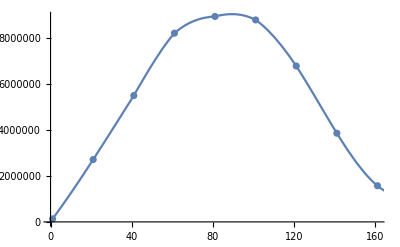

InterpolatingFunction::dmval: Input value {314.427} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {170.433} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.100809

```mathematica
avsangle = plotAVS[boat, 0.01]
```

```mathematica
momentrender[boat,boatmass[boat, N[0.1,1]],boatcom[boat,N[0.1,1]],N[0.1,1],N[30,1]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-11.0987

{0.,1.93134,0.}

{-661128.,1.14511×10^6,0.}

1349.24

-Graphics3D-